Generalized Pauli Operators: Implementation |

Consider  a system of d-level quantum system (i.e., a qudit). The canonical basis of its Hilbert space is {0,1,2,…,d-1}. Let Z:z↦z ω^z and X:z↦z+1 be the generalized Pauli operators, where z=0,1,2,…,d-1 and ω:=exp(2π ⅈ/d). Then, the Weyl-Heisenberg basis is the generating set of the generalized Pauli group,
	𝒫_d:={ω^c X^a Z^b:a,b,c=0,1,2,…,d-1}.

Here, we illustrate how to implement generalized Pauli operators of degree d=2^n with a quantum register of n qubits.

Weylpaclet:QuantumMob/Q3/ref/WeylQuantumMob Package Symbol | A genralized Pauli operator
TheWeylpaclet:QuantumMob/Q3/ref/TheWeylQuantumMob Package Symbol | The matrix represenation of a generalized Pauli operator
WeylBasispaclet:QuantumMob/Q3/ref/WeylBasisQuantumMob Package Symbol | The Weyl-Heisenberg basis

Q3 functions related to this topic.

Make sure that Q3 is loaded.

```mathematica
Needs["QuantumMob`Q3`"]
```

Choose a symbol for the quantum register.

```mathematica
Let[Qubit,S]
```

```mathematica
$n=4;
$N=Power[2,$n];
SS=S[Range@$n,$]
```

{S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

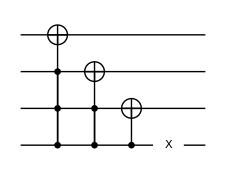

```mathematica
xx=Table[CNOT[S@Range[k+1,$n],S[k]],{k,1,$n-1}];
xx=Append[xx,S[$n,1]];
qcX=QuantumCircuit@@xx
```

```mathematica
matX=Matrix[qcX];
matX//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
in=Basis[S@{1,2,3,4}]
```

{0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))}

```mathematica
out=qcX**in
```

{0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))}

```mathematica
Thread[in->out]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))
0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))
0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))
0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))
0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))
0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))
0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))
0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))→1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))
1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))
1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))→1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))
1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))→1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))
1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))→1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))
1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))
1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))→1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))
1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))→1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))
1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))

```mathematica
ang=2Pi/$N;
zz=Table[Phase[ang*Power[2,$n-k],S[k,3]],{k,1,$n}];
qcZ=QuantumCircuit[zz]
```

-Graphics-

```mathematica
matZ=Matrix[N@qcZ]//IntegerChop;
matZ//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.707107+0.707107 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.382683+0.92388 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.382683+0.92388 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.707107+0.707107 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.92388-0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.707107-0.707107 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.382683-0.92388 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.382683-0.92388 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.707107-0.707107 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.92388-0.382683 ⅈ)

```mathematica
phs=Diagonal[matZ]//Normal//Arg;
Mod[$N*phs/(2 Pi),$N]//IntegerChop
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪K. Kawabata, T. Numasawa and S. Ryu (2023)https://doi.org/10.1103/PhysRevX.13.021007, Physical Review X 13, 021007, "Entanglement Phase Transition Induced by the Non-Hermitian Skin Effect."
▪D. Gross, Journal of Mathematical Physics 47, 122107 (2006)https://doi.org/10.1063/1.2393152, "Hudson's theorem for finite-dimensional quantum systems."
▪T. Singal et al., Quantum 7, 1048 (2023)https://doi.org/10.22331/q-2023-07-06-1048, "Counting stabiliser codes for arbitrary dimension."
▪D. Gottesman, A. Kitaev, and J. Preskill, Physical Review A 64, 012310 (2001)https://doi.org/10.1103/PhysRevA.64.012310, "Encoding a qubit in an oscillator."
▪J. Tolar, Journal of Physics: Conference Series 1071, 012022 (2018)https://doi.org/10.1088/1742-6596/1071/1/012022, "On Clifford groups in quantum computing."
▪M. M. Wolf, PhD Thesis (2003)https://www-m5.ma.tum.de/foswiki/pub/M5/Allgemeines/PublicationsWolf/thesismerge.pdf, "Partial Transpose in Quantum Information Theory."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).